```mathematica
a=1;F[x_]:=2*(Q q)/(4 Pi xi r^2) Cost-(Q q)/(4 Pi xi x^2);
r=Sqrt[a^2/4+(x-Sqrt[3]/2 a)^2];
Cost=(x-Sqrt[3]/2 a)/r;
f[x_]=D[F[x],x]//Expand//FullSimplify
```

(q Q (-5 x^3+8 √3 x^4-8 x^5+4 (1-√3 x+x^2)^(5/2)))/(8 π x^3 (1-√3 x+x^2)^(5/2) xi)

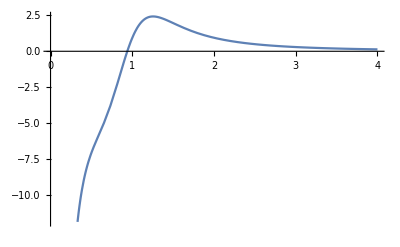

```mathematica
a=1;F[x_]:=2*(Q q)/(4 Pi xi r^2) Cost-(Q q)/(4 Pi xi x^2);
r=Sqrt[a^2/4+(x-Sqrt[3]/2 a)^2];
Cost=(x-Sqrt[3]/2 a)/r;
Q=4 Pi xi/q;
Plot[F[x],{x,0,4}]
```